## Solve for voltage when given gap size (general)

```mathematica
ClearAll;
k = 0.1;
g=30;
ep = 50;
A = 1;
x=10.8353;
Fe=(1*ep*A*V^2)/(2*(x)^2);
Fd:=k*(g-x);
Solve[{Fd==Fe,V>0},V]
```

{{V→3.}}

## Solve for position when given voltage (general)

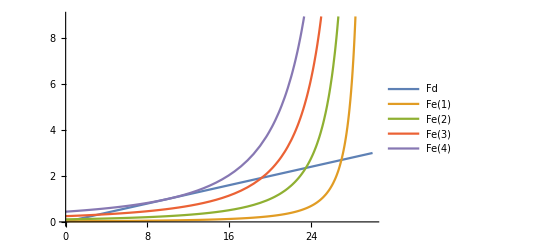

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→3.11224}}

```mathematica
ClearAll["Global`*"];
k = 0.1;
g=30;
ep = 50;
A = 1;
Fe[V_]:=(1*ep*A*V^2)/(2*(g-x)^2);
Fd = k*x;
Plot[{Fd,Fe[1],Fe[2],Fe[3],Fe[4]},{x,0,30},PlotLegends->"Expressions"]
Solve[{Fd==Fe[3],x<=g/3},x]
```

## What is Cdv/dt compared to VdC/dt?

## Solve for change in capacitance when 1v change in voltage using numbers from ideal fabrication

### Actual Variables

```mathematica
ClearAll["Global`*"];
ep = 8.85*10^-12;
b5w = 576*10^-6;
t = 2.5*10^-6;
A = b5w*t;
g0 = 1.2*10^-6;
gdc = 1.2*10^-6;
k = 1;
V1 = 1;
V2 = 2;
```

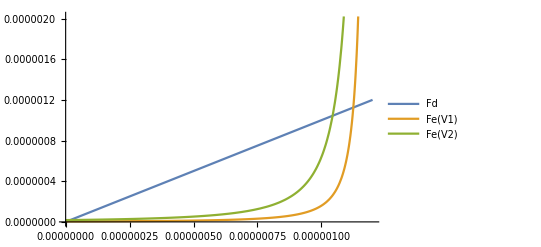

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→4.45806×10^-9}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→1.82509×10^-8}}

```mathematica
Fe[V_]:=(1*ep*A*V^2)/(2*(g0-x)^2);
Fd = k*x;

Plot[{Fd,Fe[V1],Fe[V2]},{x,0,g0},PlotLegends->"Expressions"]
Solve[{Fd==Fe[V1],x<=g0/3},x]
Solve[{Fd==Fe[V2],x<=g0/3},x]
```

```mathematica
C1=(ep*A)/(g0-4.458*10^-9)
C2 = (ep*A)/(g0-1.825*10^-8)
```

1.06596×10^-14

1.0784×10^-14

```mathematica
C2-C1
```

1.24406×10^-16

C dv/dt >> V dc/dt